The decode function can be used to transform a single graph string in the minbaum format into a Mathematica graph

```mathematica
Decode[l_]:=Graph[Join[{1<->2,1<->3,1<->4},Decode[l,2,<|2->1,3->1,4->1|>]]];
Decode[{},_,_]:={};
Decode[l_,i_,a_]:=Join[i<->#&/@#,Decode[#2,i+1,Merge[{<|#->1&/@#|>,a},Total]]]&@@TakeDrop[l,3-Lookup[a,i,0]]
```

Simple way of reading in a table, it’s stored entirely in RAM though, this might be a problem.

```mathematica
c16=ReadByteArray["Codes_16.03.03"];
```

Alternatively the codes can also be streamed, which has constant memory usage

```mathematica
c22=OpenRead["Codes_22.03.03",BinaryFormat->True]
```

InputStream[…]

Example for how to use this to find the smallest cubic graph without a Hamiltonian Path

```mathematica
Parallelize[Select[Range[1,Length[c16],21],FindHamiltonianPath[#]=={}&@Decode[Normal[c16[[#;;#+21-1]]]]&]]
```

{2164}

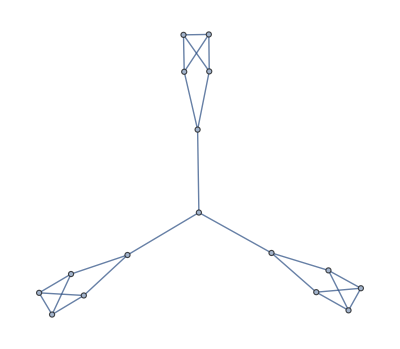

```mathematica
Decode[Normal[c16[[#;;#+21-1]]]]&[2164]
```

```mathematica
(*Length[c22]*)219583410/30
```

7319447

```mathematica
FactorInteger[%]
```

{{439,1},{16673,1}}

And an example of how to successively read and process chunks to prove that there is no cubic graph without hamilton path that is also more than 1 connected

```mathematica
For[i=0,i<439,i++,
sl=BinaryReadList[c22,"Byte",30*16673];
ParallelMap[If[VertexConnectivity[#]>1&&FindHamiltonianPath[#]=={}&@Decode[#],Print[#]]&@sl[[#;;#+30-1]]&,Range[1,Length[sl],30]];
Print[i->Date[]]
]
```